```mathematica
(*MIGUEL ANGEL NAVARRO ARENAS
1. Implemente un módulo en Mathematica que,tomando como entrada un AFD proporcione
como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD
mediante entrada paralela.
2. Implemente un módulo Mathematica que,tomando como entrada una cadena arbitraria,un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de
frontera q S,proporcione como salida True si el AC acepta la cadena y False en caso
contrario.
3. Implemente un módulo Mathematica que muestre la secuencia de computación que se
lleva a cabo en el módulo propuesto en la actividad (2) mediante un diagrama espaciotemporal.(Nota:Utilice las funciones ArrayPlot y ListAnimate explicados en la práctica de Fundamentos Básicos)
*)
automataEjemplo= {{q, p, r}, {a, b}, {{q, a, p}, {q, b, r}, {p, a, r}, {p, b, q}, {r, a, r}, {r, b, r}}, q, {r}}
```

{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}

```mathematica
AutomataCelular[automataFD_]:=Module[{states,simbols, transitions,init, finals,i,j,automataSalida},
automataSalida = {};
states=automataFD[[1]];
simbols=automataFD[[2]];
transitions=automataFD[[3]];
init=automataFD[[4]];
finals=automataFD[[5]];
For[i=1, i<=Length[states], i++,
For[j=1, j<=Length[states], j++,
AppendTo[transitions,{states[[i]],states[[j]],states[[j]]}];
];];
For[i=1, i<=Length[simbols], i++,
For[j=1, j<=Length[simbols], j++,
AppendTo[transitions,{simbols[[i]],simbols[[j]],simbols[[j]]}];
];];
automataSalida={Union[states,simbols],transitions,finals};
Return[automataSalida];
]
```

```mathematica
autCel=AutomataCelular[automataEjemplo]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

```mathematica
AutomataReconocedor[aCelular_List,palabra_List,q_]:=Module[{transitions,i,p,nextState,transition},
transitions = aCelular[[2]];

p=palabra;
transition=Cases[transitions,{q,First[palabra],_}];

p=Drop[p,1];
For[i=1,i<=Length[palabra]-1, i++,
transition =Cases[transitions,{transition[[1,3]],First[p],_}];
p=Drop[p,1];
];
If[MemberQ[aCelular[[3]],transition[[1,3]]],Return[True],Return[False]];
]
```

```mathematica
AutRec = AutomataReconocedor[autCel,{a,b,a,a,b},q]
```

True

```mathematica
AutRec2 = AutomataReconocedor[autCel,{a,b,a,b,a,b},q]
```

False

```mathematica
SecuenciaAC[aCel_List,word_List,qe_]:=Module[{palabra,palabraToEstados,transiciones,estados,pal,transicion,i,estadoAnterior},
palabra ={word};
pal=word;
palabraToEstados = {word};
estadoAnterior=qe;
transiciones=aCel[[2]];
estados={ArrayPlot[{}]};
estados = AppendTo[estados, ArrayPlot[palabra,ColorRules->{a->Red,b->Blue,q->Yellow,p->Purple,r->Green},Mesh->True]];

For[i =1, i<=Length[word],i++,
If[i==1,


(*true*)
transicion=Cases[transiciones,{qe,First[palabra[[1]]],_}];
palabraToEstados[[1,1]]=transicion[[1,3]];
AppendTo[estados, ArrayPlot[palabraToEstados,ColorRules->{a->Red,b->Blue,q->Yellow,p->Purple,r->Green},Mesh->True]];
pal=Drop[pal,1];
palabra={pal};
estadoAnterior=transicion[[1,3]];,


(*false*)
transicion=Cases[transiciones,{estadoAnterior,First[palabra[[1]]],_}];
palabraToEstados[[1,i]]=transicion[[1,3]];
AppendTo[estados, ArrayPlot[palabraToEstados,ColorRules->{a->Red,b->Blue,q->Yellow,p->Purple,r->Green},Mesh->True]];
pal=Drop[pal,1];
palabra={pal};
estadoAnterior=transicion[[1,3]];
];

];
Print[estados];
Return[ListAnimate[estados]];
];
```

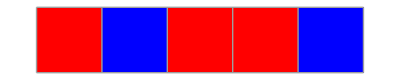
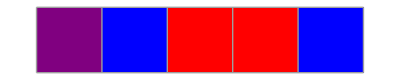
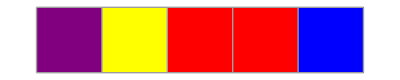
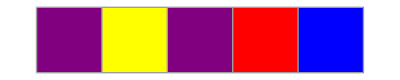
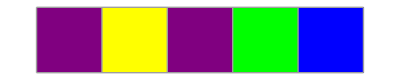
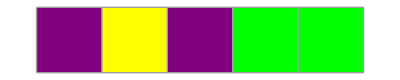
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SecuenciaAC[autCel,{a,b,a,a,b},q]
```

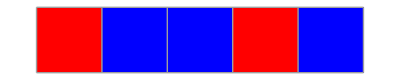
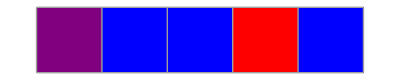
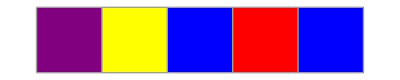
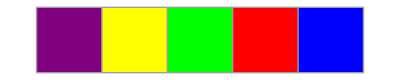
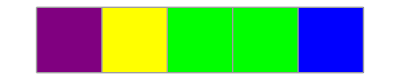
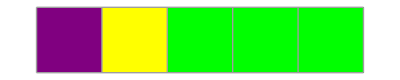
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SecuenciaAC[autCel,{a,b,b,a,b},q]
```